(6 √2 ⅇ^(-81/4+(ⅈ ((30-54 ⅈ)+x)^2)/(2 (-72 ⅈ+t))))/(√(72+ⅈ t))

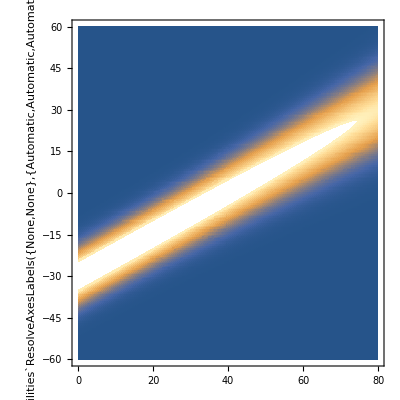

-Graphics-

```mathematica
ћ=1;
m=1;
a=12;
v=3/4;
p0=m v;
x0=-30;
ψ0[x_]:=Exp[-((x-x0)/a)^2+ⅈ p0(x-x0)/ћ]
ϕ0[p_]:=InverseFourierTransform[ψ0[x],x,p]
ϕ[t_,p_]:=ϕ0[p]Exp[-ⅈ p^2 t/(2m ћ)]
ψ[t_,x_]=FourierTransform[ϕ[t,p],p,x]
time=80;
space=60;

DensityPlot[Abs[ψ[t,x]]^2,{t,0,time},{x,-space,space},PlotPoints->150]
DensityPlot[Abs[Re[ψ[t,x]]],{t,0,time},{x,-space,space},PlotPoints->150]

Animate[Show[Plot[Abs[ψ[t,x]]^2,{x,-space,space},PlotRange->{0,ψ[0,x0]^2},Filling->Axis,PlotPoints->50],BoxRatios->Automatic],{t,0,time},AnimationRate->time/10, AnimationRunning->False,RefreshRate->60]
Animate[Show[Plot[{Re[ψ[t,x]],Im[ψ[t,x]]},{x,-space,space},PlotRange->{-ψ[0,x0],ψ[0,x0]},Filling->Axis,PlotPoints->50],BoxRatios->Automatic],{t,0,time},AnimationRate->time/10, AnimationRunning->False,RefreshRate->60]
```